```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dropBoxfolderLaptop=FileNameJoin[{"/","home","karl","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,18-03-01,18-03-02,18-03-03,18-03-06_RubidiumOnWalls,18-03-18_100mTorrBGP,18-03-22_Ei=37eV,18-03-23_pumpScan,18-03-24_higherTemps350mTorr,18-03-25_springBreakDataReview,dataDump,POL2018-03-18.dat,pumpQWP,temp,test.png,wavemeterOffsets}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-03-18_100mTorrBGP","data"}]];
polFileNames=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];
excitationFileNames=FileNames[StringExpression["EX",__,"_",__,DigitCharacter,".dat"]]
```

{EX2018-03-18_021149.dat,EX2018-03-18_021318.dat,EX2018-03-18_042007.dat,EX2018-03-18_052845.dat,EX2018-03-18_064305.dat,EX2018-03-18_075144.dat,EX2018-03-18_090558.dat,EX2018-03-18_101436.dat,EX2018-03-18_112902.dat,EX2018-03-19_001900.dat,EX2018-03-19_004104.dat,EX2018-03-19_015629.dat,EX2018-03-19_030510.dat,EX2018-03-19_042024.dat,EX2018-03-19_052911.dat,EX2018-03-19_064414.dat,EX2018-03-19_075259.dat,EX2018-03-19_090755.dat,EX2018-03-19_101639.dat,EX2018-03-19_105809.dat,EX2018-03-19_110123.dat,EX2018-03-19_110504.dat,EX2018-03-19_110857.dat,EX2018-03-19_120957.dat,EX2018-03-19_121428.dat,EX2018-03-19_121708.dat,EX2018-03-19_123813.dat,EX2018-03-19_131949.dat,EX2018-03-19_145937.dat,EX2018-03-19_161426.dat,EX2018-03-21_002337.dat,EX2018-03-21_014405.dat,EX2018-03-21_023606.dat,EX2018-03-21_035623.dat,EX2018-03-21_044819.dat,EX2018-03-21_060839.dat,EX2018-03-21_070036.dat,EX2018-03-21_082110.dat,EX2018-03-21_091308.dat,EX2018-03-21_103336.dat,EX2018-03-21_131018.dat,EX2018-03-21_132814.dat,EX2018-03-21_134126.dat,EX2018-03-21_134407.dat}

```mathematica
runFiles={
<|"exfn"->"042007","polFile"-> "042230","aouts"-> {408},"stringId"->"Ei=100_BGP=100_Eh=33"|>
};
run=runFiles[[1]];
stringId=run["stringId"]
runs=7; (*The number of Electron Polarization Runs*)
aouts=run["aouts"]; (* A list of the AOUTs or energies at which we collected data*)
pumpLights={"noPump","s+Pump","s-Pump"};
energies=aouts;
temperatures={93,96,99,102};

aoutToEnergy=GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames,run["exfn"]];
For[i=1,i≤Length[aouts],i++,energies[[i]]=aoutToEnergy[aouts[[i]]]];
firstSignalFileIndex=GetIndexOfFilenameFromTimestamp[polFileNames,run["polFile"]]

fileNames=<||>;
allFiles=<||>;

(*categories=<|"temps"->temperatures,"energies"->energies,"pumpLights"->pumpLights|>*)
categories=<|"temp"->temperatures,"pumpLight"->pumpLights|>
signalFiles=Dataset[OrganizeFilesByCategories[polFileNames,firstSignalFileIndex,categories,runs]]

allStokes=<||>;

For[m=1,m≤Length[categories[[1]]],m++,
For[i=1,i≤Length[categories[[2]]],i++,
signalFileNames=Flatten[Normal[signalFiles[Select[#cat1==categories[[1]][[m]]&]][Select[#cat2==categories[[2]][[i]]&]][All,"fileNames"]]];
stokes=CalculateAverageStokesFromFiles[signalFileNames,20.4*π/180,66.0*π/180,1.65];
AppendTo[stokes,Keys[categories][[2]]->categories[[2]][[i]]];
AppendTo[stokes,Keys[categories][[1]]->categories[[1]][[m]]];
AppendTo[stokes,"stringId"->run["stringId"]];
AppendTo[allStokes,signalFileNames[[1]]->stokes];
];
];
d=Dataset[allStokes]
```

Ei=100_BGP=100_Eh=33

2

<|temp→{93,96,99,102},pumpLight→{noPump,s+Pump,s-Pump}|>

Dataset[<>]

Dataset[<>]

## Plot Stokes Parameters with Pump Lights in Different Colors for each energy

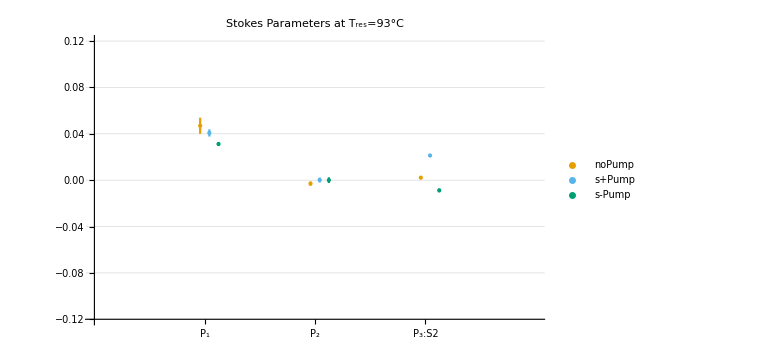
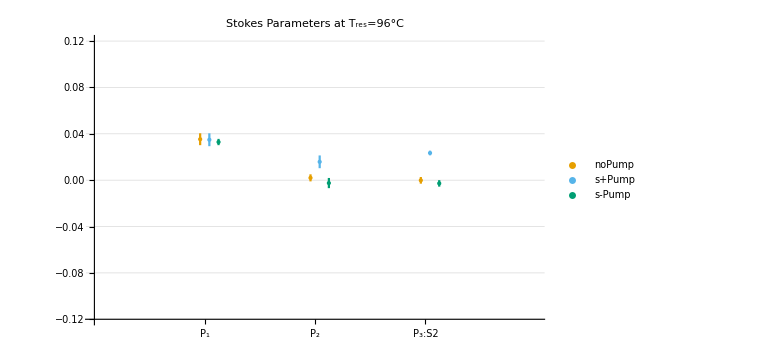
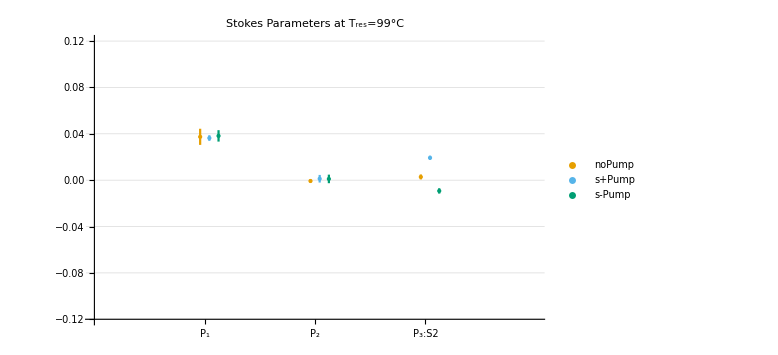
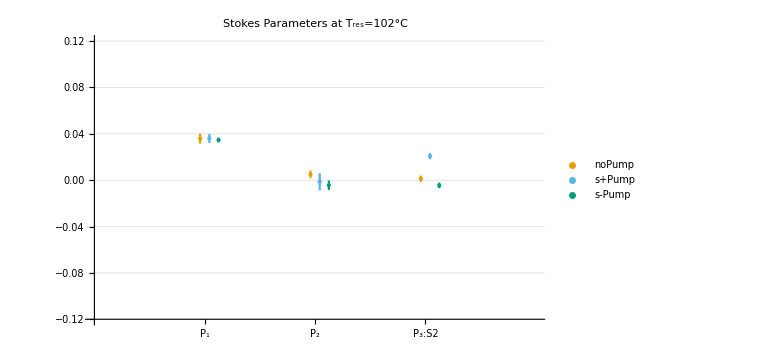
<|93→-Graphics-,96→-Graphics-,99→-Graphics-,102→-Graphics-|>

```mathematica
energyPlots=<||>;
energyPlotsShort=<||>;

chosenStokes={"p1","p2","p3_s2"};
energy=1;
pumpLight=3;
For[m=1,m≤Length[categories[[1]]],m++,(*Energies*)
plots={};
plotsShort={};
dChooseCat1=d[Select[#[Keys[categories][[1]]]==categories[[1]][[m]]&]];
For[i=1,i≤Length[categories[[2]]],i++,(* Pump Lights *)
plotData={};
plotDataShort={};
dChooseCat2=dChooseCat1[Select[#[Keys[categories][[2]]]== categories[[2]][[i]]&]];
s=GetStokesFromDatasetLine[dChooseCat2];
For[k=2,k≤Length[s[[1]]],k++,
AppendTo[plotData,{{k-1-.5((Length[categories[[2]]]-i)/Length[categories[[2]]]),s[[1]][[k]]},ErrorBar[s[[2]][[k]]]}];
];
For[k=1,k≤Length[chosenStokes],k++,
AppendTo[plotDataShort,{{k-.25((Length[categories[[2]]]/2-i)/Length[categories[[2]]]),s[[1]][chosenStokes[[k]]]},ErrorBar[s[[2]][chosenStokes[[k]]<>"err"]]}];
];
height=.12;

AppendTo[plots,ErrorListPlot[Legended[plotData,Keys[stokes][[i]]],GridLines->Automatic,ImageSize->{960,600},AxesOrigin->{0,-height},PlotRange->{{0,6},{-height,height}},PlotStyle->colorBlindPallete[[i]],Frame->False,Ticks->{{{1,"P_1"},{2,"P_2"},{3,"|P_3|"},{4,"P_3:C2"},{5,"P_3:S2"}},Automatic}]];

AppendTo[plotsShort,ErrorListPlot[Legended[plotDataShort,pumpLights[[i]]],GridLines->Automatic,ImageSize->{960,600},AxesOrigin->{0,-height},PlotRange->{{0,4},{-height,height}},PlotStyle->colorBlindPallete[[i]],Frame->False,Ticks->{{{1,"P_1"},{2,"P_2"},{3,"P_3:S2"}},Automatic}]];

];
AppendTo[energyPlots,
categories[[1]][[m]]->Show[plots,ImageSize->Large,PlotLabel->"Stokes Parameters at T_res="<>ToString[categories[[1]][[m]]]<>"°C"]
];
AppendTo[energyPlotsShort,
categories[[1]][[m]]->Show[plotsShort,ImageSize->Large,PlotLabel->"Stokes Parameters at T_res="<>ToString[categories[[1]][[m]]]<>"°C"]
];
];
For[i=1,i≤Length[energyPlots],i++,
Export["../analysis/pumpLights_Energy="<>ToString[Keys[energyPlotsShort][[i]]]<>"_"<>stringId<>".png",energyPlotsShort[[i]],ImageResolution->200];
];
(*energyPlots*)
energyPlotsShort
```

## Plot Individual Stokes Parameters as a Function of Electron Energy

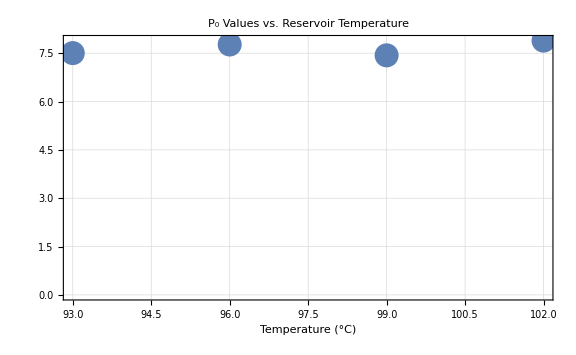
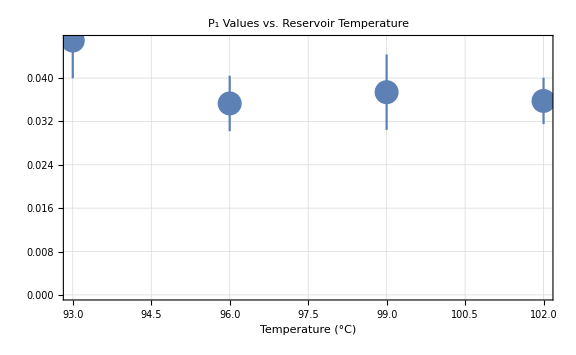
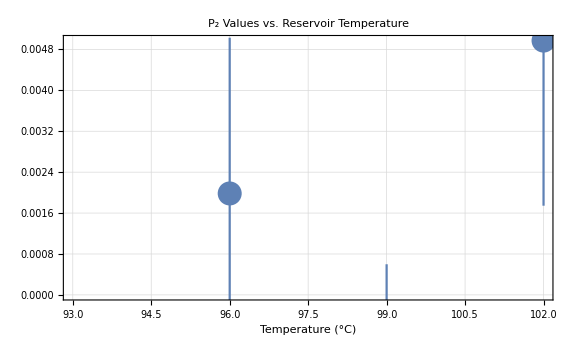
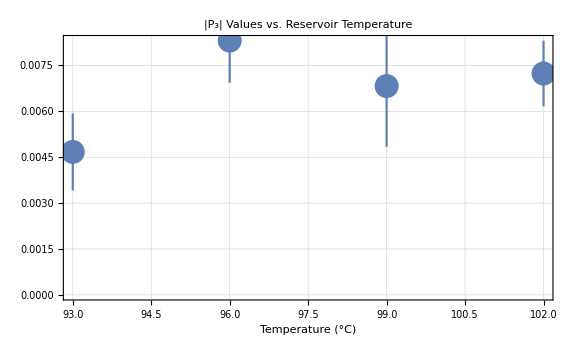
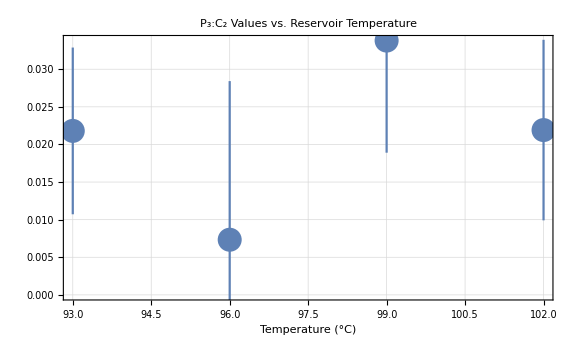
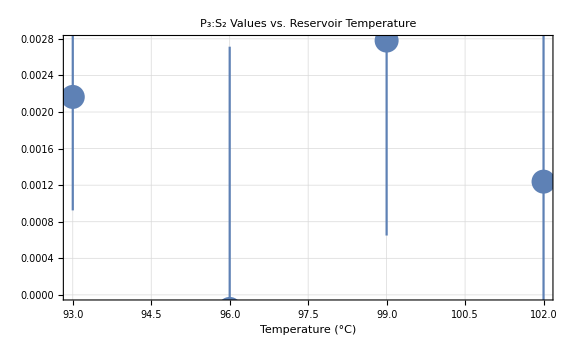
<|P_0→-Graphics-,P_1→-Graphics-,P_2→-Graphics-,|P_3|→-Graphics-,P_3:C_2→-Graphics-,P_3:S_2→-Graphics-|>

<|pumpLight→noPump,P_0→{{{93,7.5037},ErrorBar[0.181808]},{{96,7.77067},ErrorBar[0.0320168]},{{99,7.43402},ErrorBar[0.170471]},{{102,7.89188},ErrorBar[0.24934]}},P_1→{{{93,0.0469128},ErrorBar[0.00695772]},{{96,0.0353158},ErrorBar[0.00512404]},{{99,0.0373926},ErrorBar[0.00695251]},{{102,0.0357823},ErrorBar[0.00428082]}},P_2→{{{93,-0.00297033},ErrorBar[0.00178474]},{{96,0.00198348},ErrorBar[0.00304577]},{{99,-0.000713755},ErrorBar[0.00131274]},{{102,0.00497311},ErrorBar[0.00322912]}},|P_3|→{{{93,0.00467437},ErrorBar[0.00125766]},{{96,0.00831392},ErrorBar[0.00138022]},{{99,0.00682732},ErrorBar[0.00198799]},{{102,0.00723817},ErrorBar[0.00107177]}},P_3:C_2→{{{93,0.0217988},ErrorBar[0.0110821]},{{96,0.00733288},ErrorBar[0.0210872]},{{99,0.0338068},ErrorBar[0.0149036]},{{102,0.021911},ErrorBar[0.0119995]}},P_3:S_2→{{{93,0.0021651},ErrorBar[0.00124103]},{{96,-0.000153492},ErrorBar[0.00286785]},{{99,0.00278116},ErrorBar[0.00213193]},{{102,0.00123859},ErrorBar[0.00271268]}}|>

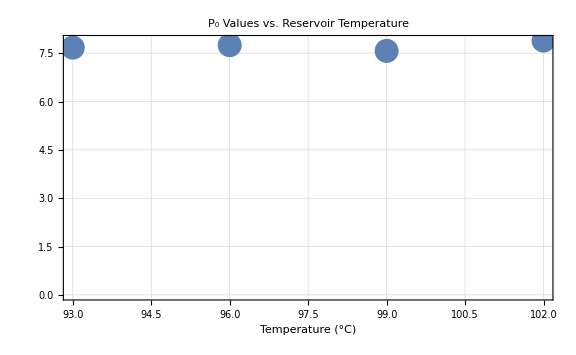
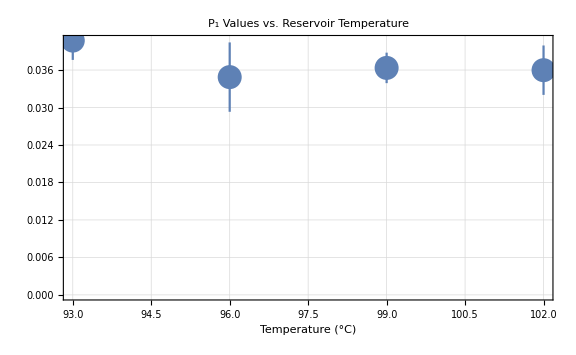
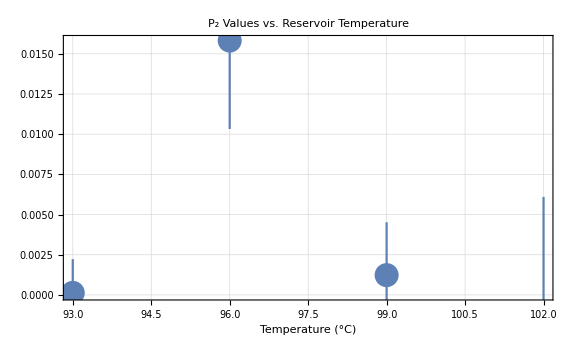
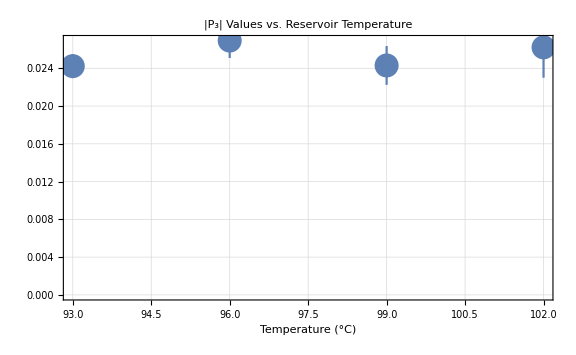
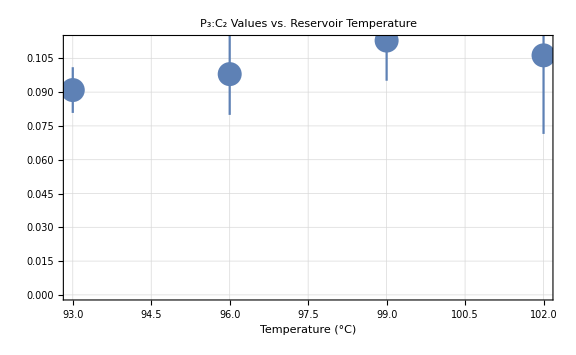
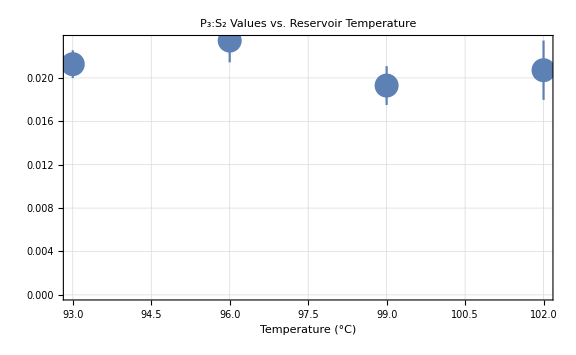
<|P_0→-Graphics-,P_1→-Graphics-,P_2→-Graphics-,|P_3|→-Graphics-,P_3:C_2→-Graphics-,P_3:S_2→-Graphics-|>

<|pumpLight→s+Pump,P_0→{{{93,7.67202},ErrorBar[0.0138959]},{{96,7.74762},ErrorBar[0.019954]},{{99,7.57017},ErrorBar[0.0144623]},{{102,7.89037},ErrorBar[0.253951]}},P_1→{{{93,0.0407161},ErrorBar[0.00309246]},{{96,0.034868},ErrorBar[0.00555293]},{{99,0.0363413},ErrorBar[0.00243983]},{{102,0.0359779},ErrorBar[0.00395427]}},P_2→{{{93,0.000126457},ErrorBar[0.00209705]},{{96,0.0158228},ErrorBar[0.00550023]},{{99,0.00123048},ErrorBar[0.00328801]},{{102,-0.00135491},ErrorBar[0.00744799]}},|P_3|→{{{93,0.0242297},ErrorBar[0.00126548]},{{96,0.0269355},ErrorBar[0.00184674]},{{99,0.0243007},ErrorBar[0.00205578]},{{102,0.0262178},ErrorBar[0.00321193]}},P_3:C_2→{{{93,0.0909109},ErrorBar[0.0101443]},{{96,0.097991},ErrorBar[0.0180966]},{{99,0.112873},ErrorBar[0.017822]},{{102,0.106315},ErrorBar[0.0348657]}},P_3:S_2→{{{93,0.021266},ErrorBar[0.00128136]},{{96,0.0234396},ErrorBar[0.00200415]},{{99,0.0192942},ErrorBar[0.00178994]},{{102,0.02071},ErrorBar[0.00273522]}}|>

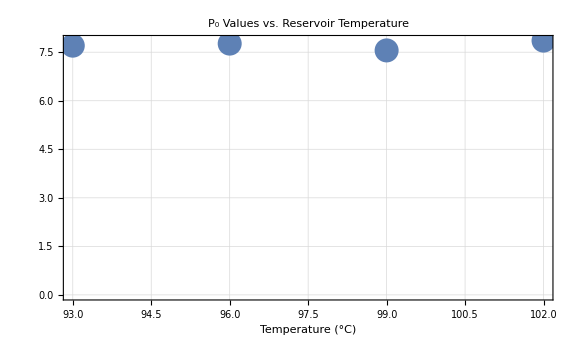
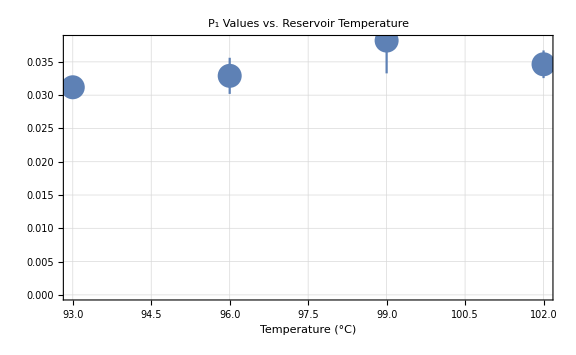
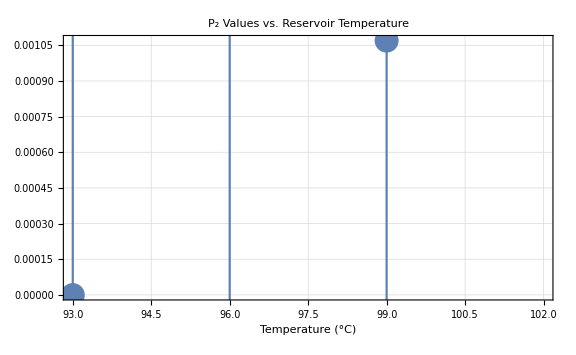
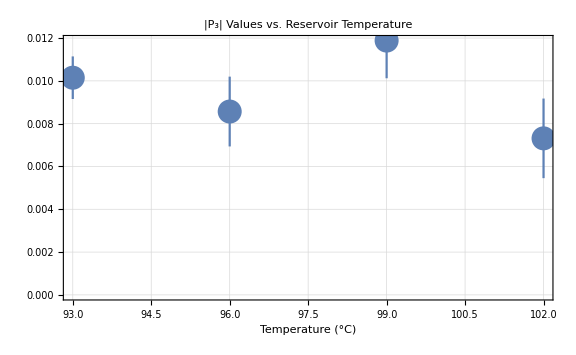
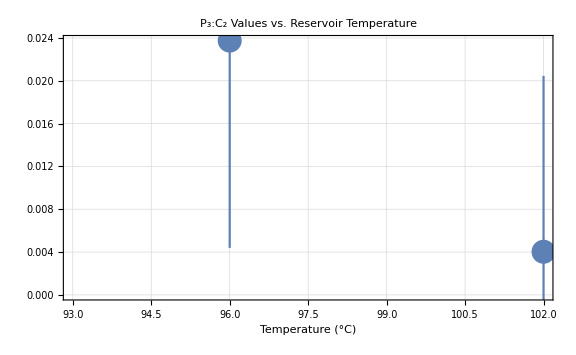
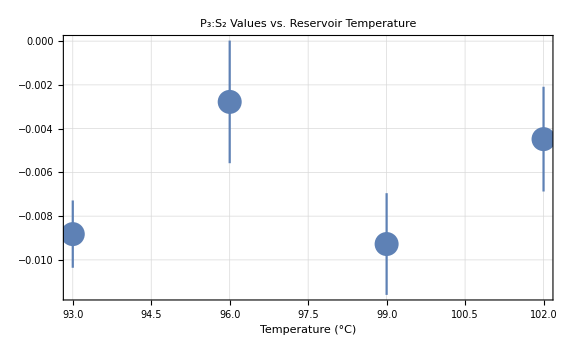
<|P_0→-Graphics-,P_1→-Graphics-,P_2→-Graphics-,|P_3|→-Graphics-,P_3:C_2→-Graphics-,P_3:S_2→-Graphics-|>

<|pumpLight→s-Pump,P_0→{{{93,7.70234},ErrorBar[0.00842897]},{{96,7.76588},ErrorBar[0.0175227]},{{99,7.555},ErrorBar[0.0332275]},{{102,7.85897},ErrorBar[0.245804]}},P_1→{{{93,0.0311841},ErrorBar[0.00145668]},{{96,0.0329013},ErrorBar[0.00271317]},{{99,0.0381961},ErrorBar[0.00492417]},{{102,0.0346368},ErrorBar[0.00207775]}},P_2→{{{93,-8.59551×10^-7},ErrorBar[0.00246659]},{{96,-0.00250172},ErrorBar[0.00439266]},{{99,0.00106985},ErrorBar[0.00369304]},{{102,-0.00435569},ErrorBar[0.00410292]}},|P_3|→{{{93,0.0101471},ErrorBar[0.000994897]},{{96,0.0085667},ErrorBar[0.0016305]},{{99,0.0118819},ErrorBar[0.00176032]},{{102,0.0073137},ErrorBar[0.00185955]}},P_3:C_2→{{{93,-0.0289064},ErrorBar[0.00838235]},{{96,0.0237554},ErrorBar[0.0193651]},{{99,-0.0432366},ErrorBar[0.0135041]},{{102,0.0040295},ErrorBar[0.0164301]}},P_3:S_2→{{{93,-0.00882156},ErrorBar[0.00153824]},{{96,-0.00277745},ErrorBar[0.00280269]},{{99,-0.00927517},ErrorBar[0.00232468]},{{102,-0.00447949},ErrorBar[0.00239408]}}|>

```mathematica
plotLabels={"P_0","P_1","P_2","|P_3|","P_3:C_2","P_3:S_2"};
energy=1;
pumpLight=2;
valueOrError=1;

plotData=<||>;
plots=<||>;

pl =1;(*Pump Light*)
For[j=1,j≤Length[pumpLights],j++,
onePump=d[Select[#pumpLight== pumpLights[[j]]&]];
AppendTo[plotData,"pumpLight"-> pumpLights[[j]]];
For[k=1,k≤ Length[stokesNames],k++, (*stokes index*)
plotPoints={};
onePumpOneStokes=onePump[All,{"temp",stokesNames[[k]],stokesErrNames[[k]]}][Values,All];
For[i=1,i≤Length[categories[[1]]],i++,(*energies*)
plotDat=onePumpOneStokes[[i]];
plotPoint={{plotDat[[1]],plotDat[[2]]},ErrorBar[plotDat[[3]]]};
AppendTo[plotPoints,plotPoint];
];
AppendTo[plotData,plotLabels[[k]]->plotPoints];
AppendTo[plots,plotLabels[[k]]->
ErrorListPlot[plotPoints,PlotRange->{0,Automatic},GridLines->Automatic,Frame->True,PlotLabel->  plotLabels[[k]]<> " Values vs. Reservoir Temperature",FrameLabel->{"Temperature (°C)",None}]]
];
Print[plots];
Print[plotData];
For[i=1,i≤Length[plots],i++,
Export["../analysis/"<>pumpLights[[j]]<>"_stokesParameter="<>stokesNames[[i]]<>"_"<>stringId<>".png",plots[[i]],ImageResolution->200];
];
Export["../analysis/stokesPlots.png",plots,ImageResolution->200]
];
```

```mathematica
Keys[allStokes]
```

{32.4584,25.0167,15.3426}

## Export TSV file with all Stokes Values

```mathematica
string="";
string=StringJoin[string,"energy\t"];
string=StringJoin[string,"Pumplight\t"];
For[a=1,a<=Length[stokesNames],a++,
string=StringJoin[string,ToString[Keys[allStokes[[1]][[1]][[1]]][[a]]]<>"\t"<>ToString[Keys[allStokes[[1]][[1]][[2]]][[a]]]<>"\t"];
];
string=StringJoin[string,"\n"];
For[b=1,b≤Length[energies],b++,

For[c=1,c≤Length[pumpLights],c++,
string=StringJoin[string,ToString[Keys[allStokes][[b]]]<>"\t"];
string=StringJoin[string,Keys[allStokes[[b]]][[c]]<>"\t"];
For[a=1,a<=Length[stokesNames],a++,
string=StringJoin[string,ToString[allStokes[[b]][[c]][[1]][[a]]]<>"\t"<>ToString[allStokes[[b]][[1]][[2]][[a]]]<>"\t"];
];
string=StringJoin[string,"\n"];
];
];
Export["tabulatedValues"<>stringId<>".txt",string];
```

## Plot Stokes Parameters vs. Energy with Pump Lights in Different Colors

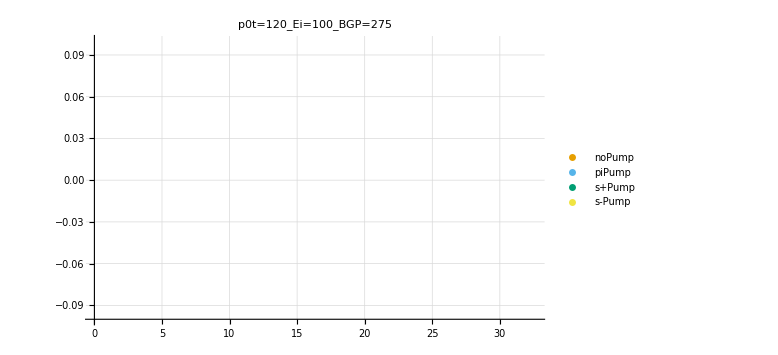
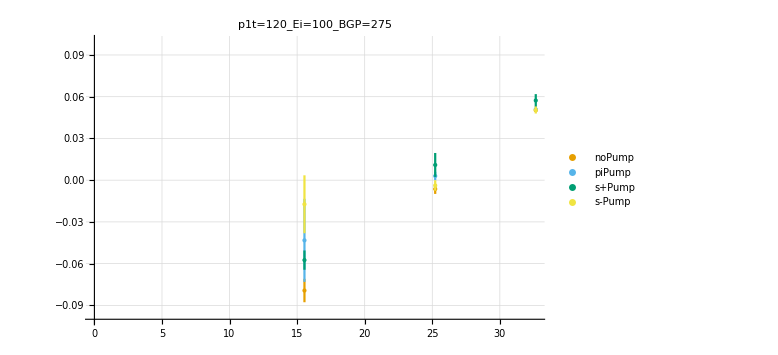
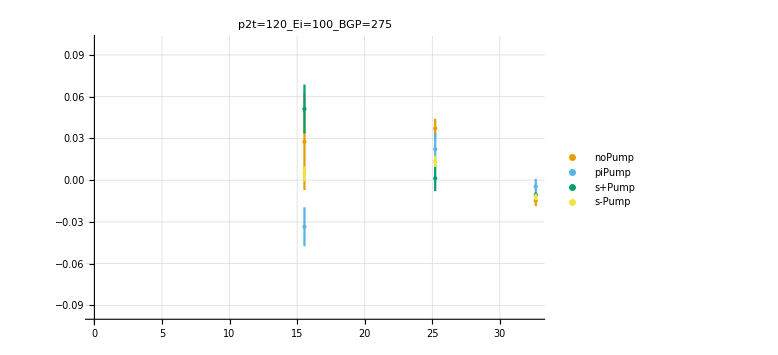
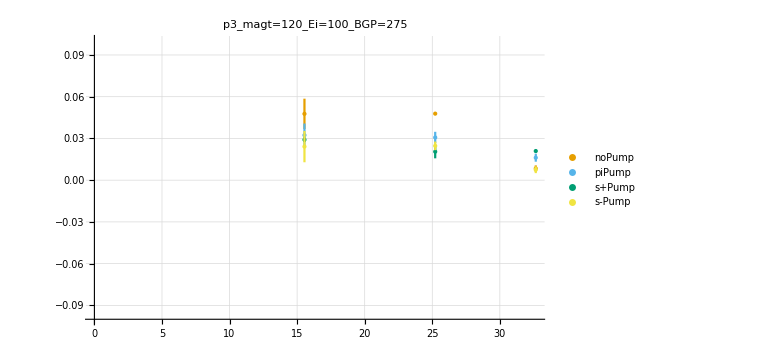
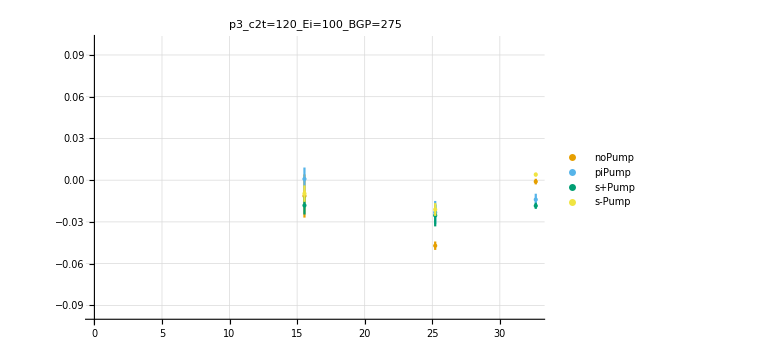
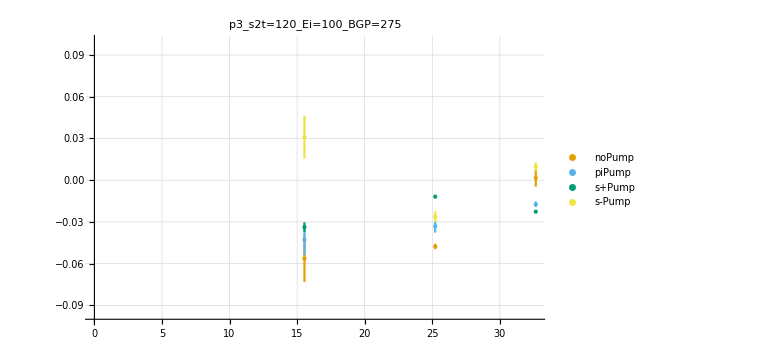
<|p0→-Graphics-,p1→-Graphics-,p2→-Graphics-,p3_mag→-Graphics-,p3_c2→-Graphics-,p3_s2→-Graphics-|>

```mathematica
stokesPlots=<||>;

energy=3;
pumpLight=4;
For[m=1,m≤Length[stokesNames],m++,
plots={};
For[i=1,i≤Length[pumpLights],i++,
plotData={};
For[k=1,k≤Length[energies],k++,
s=allStokes[[k]][[i]];
AppendTo[plotData,{{energies[[k]],s[[1]][[m]]},ErrorBar[s[[2]][[m]]]}];
];
height=.1;
AppendTo[plots,ErrorListPlot[Legended[plotData,pumpLights[[i]]],GridLines->Automatic,ImageSize->{960,600},AxesOrigin->{0,-height},PlotRange->{Automatic,{-.1,.1}},PlotStyle->colorBlindPallete[[i]],Frame->False]];
];
AppendTo[stokesPlots,
stokesNames[[m]]->Show[plots,ImageSize->Large,PlotLabel->stokesNames[[m]]<>stringId]
];
];
For[i=1,i≤Length[stokesPlots],i++,
Export[stokesNames[[i]]<>"_"<>stringId<>".png",stokesPlots[[i]],ImageResolution->200];
];
stokesPlots
```

## Display all raw data and averages

Pump Light: noPump, Energy: 32.4584

-Graphics-

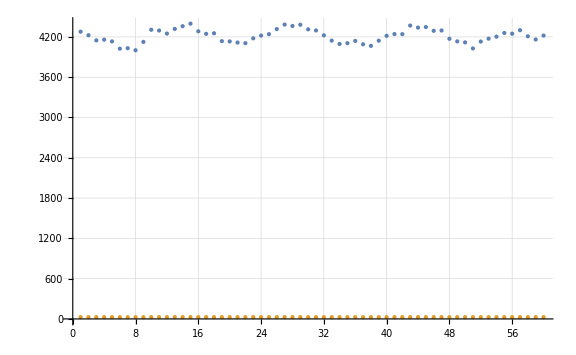

Pump Light: piPump, Energy: 32.4584

-Graphics-

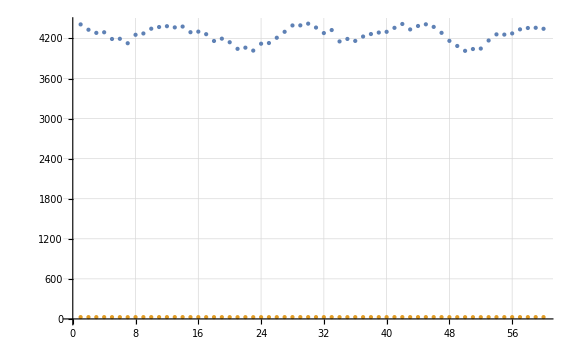

Pump Light: s+Pump, Energy: 32.4584

-Graphics-

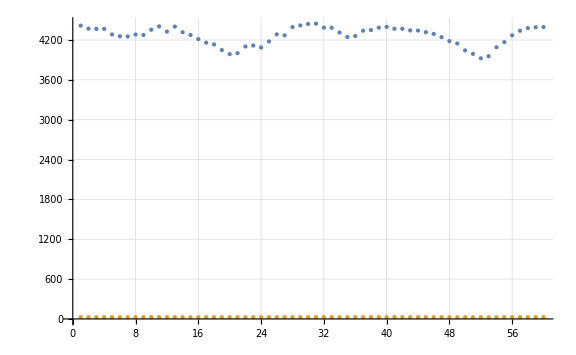

Pump Light: s-Pump, Energy: 32.4584

-Graphics-

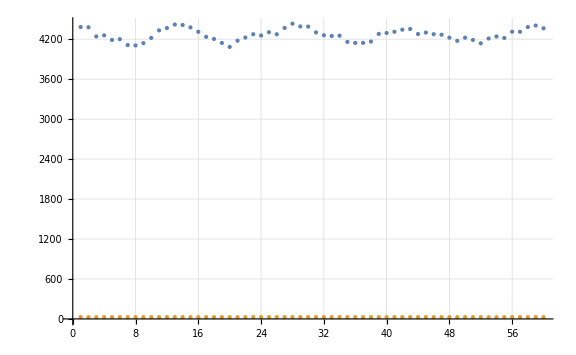

Pump Light: noPump, Energy: 25.0167

-Graphics-

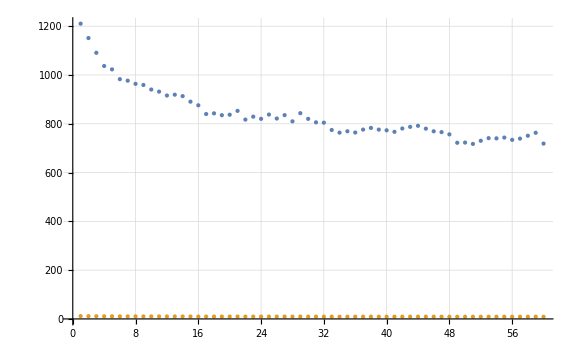

Pump Light: piPump, Energy: 25.0167

-Graphics-

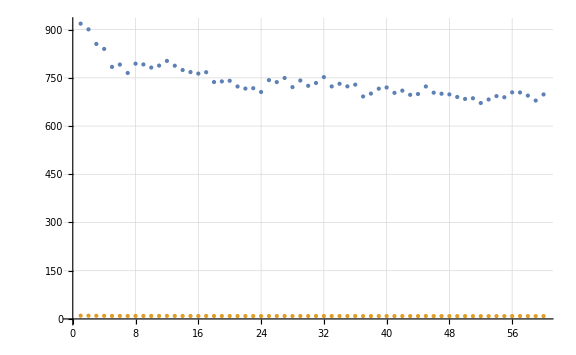

Pump Light: s+Pump, Energy: 25.0167

-Graphics-

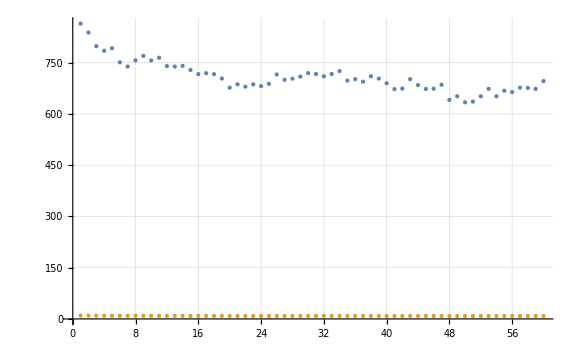

Pump Light: s-Pump, Energy: 25.0167

-Graphics-

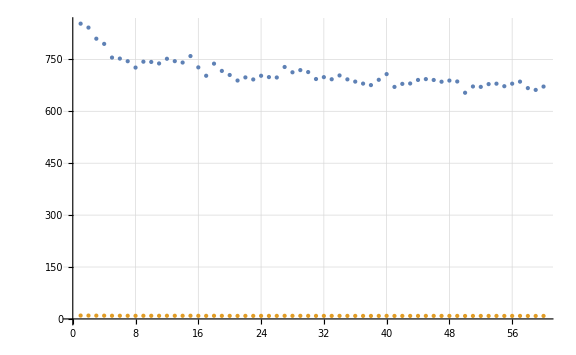

Pump Light: noPump, Energy: 15.3426

-Graphics-

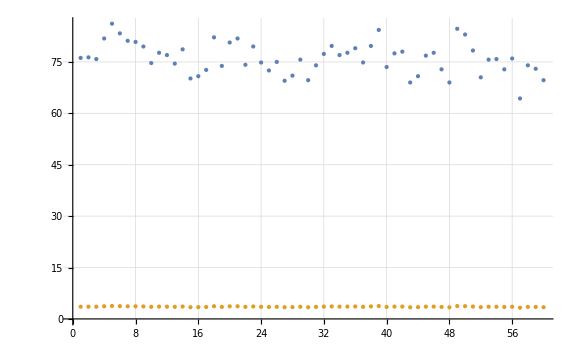

Pump Light: piPump, Energy: 15.3426

-Graphics-

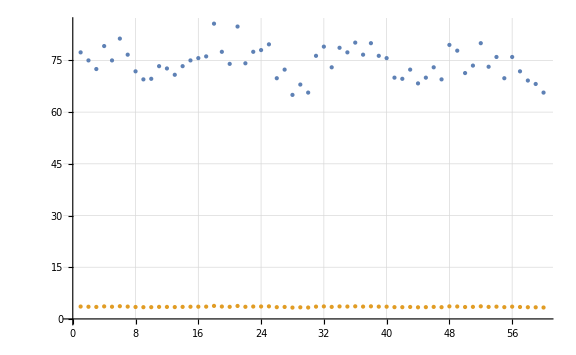

Pump Light: s+Pump, Energy: 15.3426

-Graphics-

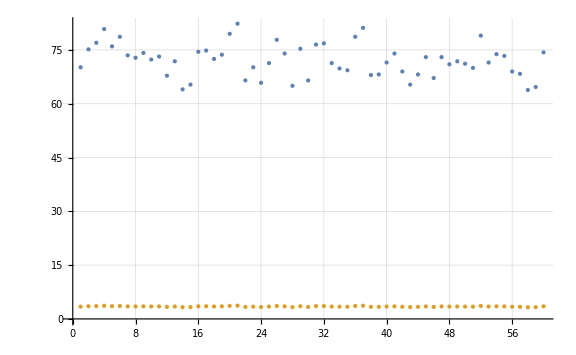

Pump Light: s-Pump, Energy: 15.3426

-Graphics-

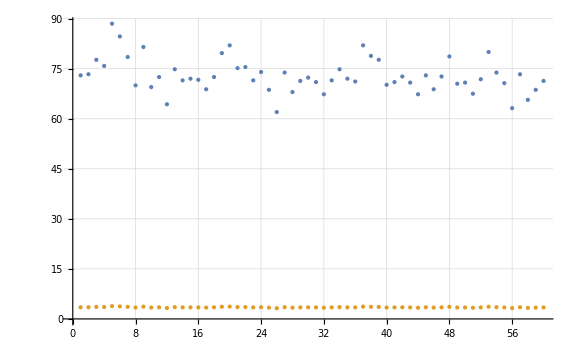

```mathematica
allStokes=<||>;
stokes=<||>;
allFiles=signalFiles;
For[j=1,j<=Length[energies],j++,
For[i=1,i<=Length[pumpLights],i++,
Print["Pump Light: "<>ToString[pumpLights[[i]]]<>", Energy: "<>ToString[energies[[j]]]]; 
fileNames=Flatten[Normal[signalFiles[Select[#cat2==pumpLights[[i]]&]][Select[#cat1==energies[[j]]&],"fileNames"]]];
Print[Rasterize[PlotListOfPolFileNames[fileNames]]];
Print[ListPlot[GetAverageCountRateFromFileNames[fileNames]]];
];
];
```

## Show representative Background Subtraction

```mathematica
darkFiles
```

Dataset[<>]

```mathematica
{{pumpStyle=1;
energy=1;
runNumber=2;
xAxisLabel="Retarder Position (60=1 Rev)";
imageRes=100;



averageDarkCounts=GetAverageCountRateFromFileNames[darkFiles[[pumpStyle]][[energy]]];
(*
molyFileNames=Flatten[Normal[molyFiles[Select[#cat2==pumpLights[[pumpStyle]]&]][Select[#cat1==energies[[energy]]&],"fileNames"]]];
molyFile=ImportFile[molyFileNames[[runNumber]]];
dwell=molyFile[[1]]["DWELL(s)"];
currentScale=molyFile[[1]]["SCALE"];

countRateData=Normal[molyFile[[2]][[All,"COUNT"]]]/dwell;
currentData=Abs[Normal[molyFile[[2]][[All,"CURRENT"]]]*10^(-currentScale)/nA];


molyMinusDark=countRateData-averageDarkCounts[[1]];
molyMinusDarkPlot=ListPlot[{Legended[averageDarkCounts[[1]],"Dark Counts\n(4 run average)"],Legended[countRateData,"Representative\nMoly Count Rate"],Legended[molyMinusDark,"Moly Minus Dark"]},PlotLabel->"Moly Count Dark Subtraction",FrameLabel->{xAxisLabel,"Count Rate"}];

molyCurrentPlot=ListPlot[currentData,PlotLabel->"Representative Moly Current",PlotRange->{Automatic,{Automatic,Automatic}},FrameLabel->{xAxisLabel,"Current (nA)"}];

molyMinusDarkCurrentNorm=molyMinusDark/currentData;
molyMinusDarkCurrentNormPlot=ListPlot[molyMinusDarkCurrentNorm,PlotLabel->"Moly Minus Dark, Current Normalized",FrameLabel->{xAxisLabel,"Count Rate, Current Normalized (Hz/nA)"}] ;

signalFileNames=Flatten[Normal[signalFiles[Select[#cat2==pumpLights[[pumpStyle]]&]][Select[#cat1==energies[[energy]]&],"fileNames"]]];
signalFile=ImportFile[signalFileNames[[runNumber]]];
dwell=signalFile[[1]]["DWELL(s)"];
currentScale=signalFile[[1]]["SCALE"];
mTorrHe=signalFile[[1]]["CVGauge(He)(Torr)"]/mTorr;

countRateData=Normal[signalFile[[2]][[All,"COUNT"]]]/dwell;
currentData=Abs[Normal[signalFile[[2]][[All,"CURRENT"]]]*10^(-currentScale)/nA];
20.5

signalMinusDark=countRateData-averageDarkCounts[[1]];
signalMinusDarkPlot=ListPlot[{Legended[countRateData,"Raw Signal\nCounts"],Legended[signalMinusDark,"Raw Signal\nMinus Dark"]},PlotLabel->"Signal Minus Dark Counts",FrameLabel->{xAxisLabel,"Count Rate (Hz)"}];

signalCurrentPlot=ListPlot[currentData,PlotLabel->"Representative Signal Current",PlotRange->{Automatic,{Automatic,Automatic}},FrameLabel->{xAxisLabel,"Current (nA)"}];

signalMinusMoly=signalMinusDark/currentData-molyMinusDarkCurrentNorm ;
signalCurrentNormSubtractionPlot=ListPlot[{Legended[signalMinusDark/currentData,"Signal Minus Dark,\nCurrent Normalized"],Legended[molyMinusDarkCurrentNorm,"Moly Counts,\nCurrent Normalized"],Legended[signalMinusMoly,"Signal Minus Moly,\nCurrent Normalized"]},PlotLabel->"Signal Background Subtraction",FrameLabel->{xAxisLabel,"Count Rate, Current Normalized (Hz/nA)"}];

grid=GraphicsGrid[{{molyMinusDarkPlot,signalMinusDarkPlot},
{molyCurrentPlot,signalCurrentPlot},
{molyMinusDarkCurrentNormPlot,signalCurrentNormSubtractionPlot}},ImageSize->{1510,Automatic}]

signalMinusMolyHeNormalized=signalMinusMoly/mTorrHe;
finalPlot=ListPlot[Legended[signalMinusMolyHeNormalized,"Signal Counts, background subtracted,\n helium pressure normalized."]]
fc=DFT[signalMinusMolyHeNormalized]
sine=1;
cosine=2;
signal=1;
error=2;
sin=fc[[sine]][[signal]];
cos=fc[[cosine]][[signal]];
sinBar=BarChart[Take[sin,{2,11}],PlotLabel->"Sin Fourier Coefficients",ChartLabels->{"S_1","S_2","S_3","S_4","etc."},Frame->True];
cosBar=BarChart[Take[cos,{2,11}],PlotLabel->"Cos Fourier Coefficients",ChartLabels->{"C_1","C_2","C_3","C_4","etc."},Frame->True];
fcPlot=GraphicsGrid[{{sinBar},{cosBar}}]
recreation[θ_]:=cos[[1]]+cos[[3]]Cos[2(θ*π/30)]+sin[[3]]Sin[2(θ*π/30)]+cos[[5]]Cos[4(θ*π/30)]+sin[[5]]Sin[4(θ*π/30)];
simulation=Plot[recreation[θ],{θ,0,60},PlotRange->{Automatic,{0,Automatic}}]
samplePol=Show[{finalPlot,simulation},PlotRange->{Automatic,{0,Automatic}},PlotLabel->"Example Polarization Data",FrameLabel-> {"Polarimeter Position (60= 1 rev)","BS, Normalized Count Rate (Hz/nA/mTorr_He)"}]
SetDirectory[ParentDirectory[]<>"/analysis"]
Export["samplePolarization.png",samplePol,ImageResolution->200]
Export["sampleFC.png",fcPlot,ImageResolution->200]
Export["backGroundSubtractionSample.png",grid,ImageResolution->100]
SetDirectory[ParentDirectory[]<>"/data"]


PlotRawPolFromFileName[molyFiles["noPump"][[1]]]
molyExample=GetCurrentNormalizedMolyCountRateFromFileNames[molyFiles["noPump"][[1]],darkCounts];
ListPlot[molyExample[[1]],PlotLabel->"Example set of Moly Counts"]
*), □}}
```

Import::chtype: First argument 32.6584 is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

StringPart::strse: String or list of strings expected at position 1 in StringPart[$Failed,1].

Import::chtype: First argument 32.6584 is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

StringPart::strse: String or list of strings expected at position 1 in StringPart[$Failed,1].

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,{1,-1},All].

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of <||> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{Null^6,□}}

```mathematica
colorBlindPallete={RGBColor[230/255,159/255,0],RGBColor[86/255,180/255,233/255],RGBColor[0/255,158/255,115/255],RGBColor[240/255,228/255,66/255],RGBColor[0/255,114/255,178/255],RGBColor[213/255,94/255,0/255],RGBColor[204/255,121/255,167/255],RGBColor[0/255,0/255,0/255]};
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large];
SetOptions[ListPlot,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic];
SetOptions[BarChart,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic];
stokesNames={"p0","p1","p2","p3_mag","p3_c2","p3_s2"};
stokesErrNames={"p0err","p1err","p2err","p3_magerr","p3_c2err","p3_s2err"};
nA=1*^-9;
mTorr=1*^-3;
alpha=20.4*π/180;
beta=68.7*π/180;
deltaAB=alpha-beta;
delta=94.54*π/180 (*Munir's reported 1.66 plus or minus .01*);

alphaOld=3.2*π/180;
betaOld=-6.95*π/180;
rev=1;

Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
(* If given a list of files*)
GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"-> "",":"->""}]->joinedWithSpaces];
,
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"->"",":"->""}]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

FourierFit[list_,rev_]:=Module[{fit,function,dataPts,stepSize,dataPtsPerRev,angles,data(*,C0,C2,C4,S2,S4*)},

function[θ_]= C0+C2 Cos[2(θ+θo)]+C4 Cos[4(θ+θo)]+S2 Sin[2(θ+θo)]+S4 Sin[4(θ+θo)];
dataPts=Length[list];
dataPtsPerRev=dataPts/rev;
angles=Range[0,(2π*rev)-2π/dataPtsPerRev,2π/dataPtsPerRev];
data=Transpose[{list,angles}];
fit=NonlinearModelFit[data,function[θ],{{C0,1000},C2,C4,S2,S4,θo},θ]
];


DFT[list_,rev_:1]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];
StokesParametersFromFourierCoefficients[fc_(*Fourrier Coefficients*),rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=Module[{c0,c2,c4,s2,s4,stokes},
stokes={0,0,0,0,0,0};
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
stokes[[1]]=c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0]);
stokes[[2]]=2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[3]]=2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[4]]=Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]]);
stokes[[5]]=c2/(Sin[delta]Sin[2 alpha + 2 beta0]stokes[[1]]);
stokes[[6]]=-s2/(Sin[delta]Cos[2 alpha + 2beta0]stokes[[1]]);
stokes];

(* 
Someday when I'm bored, I can try to implement the asoociation version of the stokes vectors. Today is not that day
StokesParametersFromFourierCoefficients[fc_(*Fourrier Coefficients*),rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=Module[{c0,c2,c4,s2,s4,stokes},
stokes=<||>;
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
AppendTo[stokes,stokesNames[[1]]->c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0])];
AppendTo[stokes,stokesNames[[2]]->2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]]];
AppendTo[stokes,stokesNames[[3]]->2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]]];
AppendTo[stokes,stokesNames[[4]]->Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]])];
AppendTo[stokes,stokesNames[[5]]->c2/(Sin[delta]Sin[2 alpha + 2 beta0]stokes[[1]])];
AppendTo[stokes,stokesNames[[6]]->-s2/(Sin[delta]Cos[2 alpha + 2beta0]stokes[[1]])];
stokes
];
*)

StokesParametersFromRawFourierData[intensityArray_,rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=
Module[{fc(*Fourrier Coefficients*),c0,c2,c4,s2,s4,stokes},
fc=DFT[intensityArray,rev];
StokesParametersFromFourierCoefficients[fc,rev,alpha,beta0,delta]
];

StokesParametersFromPolFile[polFile_,alpha_,beta0_,delta_,rev_]:=
Module[{intensityArray,f},
intensityArray=Normal[polFile[[2]][All,"COUNT"]];
StokesParametersFromRawFourierData[intensityArray,rev,alpha,beta0,delta]
];

StokesParametersFromPolFileName[polFileName_,alpha_,beta0_,delta_]:=
Module[{intensityArray,f,rev},
f=ImportFile[polFileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
rev=f[[1]]["REV"];
StokesParametersFromPolFile[f,alpha,beta0,delta,rev_]
];

GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];



GetAverageCountRateFromFileNames[fileNames_]:=Module[{files},
files=ImportFile[fileNames];
GetAverageCountRateFromFiles[files]
];

(* See Nate Clayburn's explanation on Background Subtraction p. 129 eq. 93*)
(* Returns a list of two items.
	the first item is a list of the intensity reaching the PMT at each step of the polarimeter.
	the second item is the standard deviation of these counts
*)
GetAverageCountRateFromFiles[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFiles[files_]:=Module[{t,scale,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,rev},
nDataPts=files[[1]][[1]]["DATAPPR"];
rev=files[[1]][[1]]["REV"];
scale=files[[1]][[1]]["SCALE"];
darkCountsRate=10;
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files]*rev;
t=dwell*nCycles;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/t/Abs[current[[j]]*10^(-scale)/(1*^-9)];
errorSum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/(t^2*(current[[j]]*10^(-scale)/(1*^-9))^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFileNames[fileNames_]:=Module[{filesPass,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
filesPass=ImportFile[fileNames];
GetCurrentNormalizedAverageCountRateFromFiles[filesPass]
];

GetCurrentNormalizedMolyCountRateFromFileNames[fileNames_,darkCountsRate_]:=Module[{files},
files=ImportFile[fileNames];
GetCurrentNormalizedMolyCountRateFromFiles[files,darkCountsRate]
];

GetCurrentNormalizedMolyCountRateFromFiles[files_,darkCountsRate_]:=Module[{currentnA,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,currentScale},
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
currentScale=files[[i]][[1]]["SCALE"];
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
currentnA=current*10^(-currentScale)/nA;
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]/dwell-darkCountsRate[[1]][[j]])/(nCycles*Abs[currentnA[[j]]]);
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*currentnA[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*currentnA[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

BackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageSignalRateCurrentNorm[files_,molyCountsRate_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,rev,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
rev=files[[i]][[1]]["REV"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/rev/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/rev/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/rev/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*rev^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*rev^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2*rev^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

SignalRateCurrentNormFromFiles[file_,molyCountFiles_,darkCountsFiles_]:=Module[{molyCountsRate,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=AverageGetAverageCountRateFromFiles[darkCountsFiles];
molyCountsRate=AverageBackgroundRateCurrentNorm[molyCountFiles,darkCountsFiles];
SignalRateCurrentNormFromRates[file,molyCountFiles,darkCountsFiles]
];
SignalRateCurrentNormFromRates::usage ="SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background."
SignalRateCurrentNormFromRates[fileName_,molyCountsRate_,darkCountsRate_]:=Module[{file,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
file=ImportFile[fileName];
nDataPts=Length[Normal[file[[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
counts=Normal[file[[2]][All,"COUNT"]];
current=Normal[file[[2]][All,"CURRENT"]];
dwell=file[[1]]["DWELL(s)"];
nCycles=file[[1]]["REV"];
mTorrHe=file[[1]]["CVGauge(He)(Torr)"]/mTorr;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=((counts[[j]]/dwell-darkCountsRate[[1]][[j]])/Abs[current[[j]]]-molyCountsRate[[1]][[j]])/(nCycles*mTorrHe);
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2*mTorrHe^2)-(darkCountsRate[[2]][[j]])^2/(nCycles^2*current[[j]]^2*mTorrHe^2)-(molyCountsRate[[2]][[j]])^2/(nCycles^2*mTorrHe^2);
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

CalculateOneFileBackgroundSubtractedStokes[polFileName_,molyCountRate_,darkCountRate_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["REV"];
signal=SignalRateCurrentNormFromRates[polFileName,molyCountRate,darkCountRate];
StokesParametersFromRawFourierData[signal[[1]],rev,alpha,beta,delta]
];

CalculateOneFileStokes[polFileName_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["REV"];
signal=GetCurrentNormalizedAverageCountRateFromFiles[{file}];
StokesParametersFromRawFourierData[signal[[1]],rev,alpha,beta,delta]
];

CalculateOneFileCurrent[polFileName_]:=Module[{signal,stokes,file,rev,currentScale,currentValues,currentPlot,currentAvg,currentStd},
file=ImportFile[polFileName];
rev=file[[1]]["REV"];
currentScale=file[[1]]["SCALE"];
currentValues=Normal[file[[2]][All,"CURRENT",Abs]]*10^(-currentScale)/nA;
currentAvg=Mean[currentValues];
currentStd=StandardDeviation[currentValues];
currentPlot=ListPlot[currentValues/currentAvg,PlotLabel->"Current, Normalized to Average Current",FrameLabel->{"Stepper Motor Position","Current (nA)"},PlotRange->{.8,1.2}];
<|"currentPlot"->currentPlot,"currentAvg"->currentAvg,"currentStd"->currentStd|>
];

AverageStokes[stokesVectors_]:=Module[{i,transposedValues,stokes,stokesStdDev},
stokes=stokesVectors[[1]];
stokesStdDev=stokes; (*Just creating another object with the same length as stokes *)
transposedValues=Transpose[stokesVectors];
For[i=1,i≤Length[stokesVectors[[1]]],i++,
stokes[[i]]=stokesNames[[i]]->Mean[transposedValues[[i]]];
stokesStdDev[[i]]=stokesErrNames[[i]]->StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]];
];
Join[Association[stokes],Association[stokesStdDev]]
];

CalculateAverageBackgroundSubtractedStokesFromFilesAndCountRates[polFileNames_,molyCountRate_,darkCountRate_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues},
stokes=<|"p0"->0,"p1"->0,"p2"->0,"p3_mag"->0,"p3_c2"->0,"p3_s2"->0|>;
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],molyCountRate,darkCountRate,alpha,beta,delta];
AppendTo[stokesValues,stokes]
];

Print[AverageStokes[stokesValues]];
AverageStokes[stokesValues]
]

CalculateAverageStokesFromFiles[polFileNames_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues,singleRunInfo,allSingleRunInfo,current,counts,countsPlot,combinedPlot,results},
stokes=<|"p0"->0,"p1"->0,"p2"->0,"p3_mag"->0,"p3_c2"->0,"p3_s2"->0|>;
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
allSingleRunInfo=<||>;
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],alpha,beta,delta];
current=CalculateOneFileCurrent[polFileNames[[j]]];
counts=GetIntensityArrayFromFileName[polFileNames[[j]]];
countsPlot=ListPlot[counts];
AppendTo[stokesValues,stokes];
singleRunInfo=<|"stokes"->stokes|>;
AppendTo[singleRunInfo,current];
AppendTo[singleRunInfo,"counts"->countsPlot];
AppendTo[allSingleRunInfo, polFileNames[[j]]->singleRunInfo];
];
combinedPlot=ListPlot[GetAverageCountRateFromFileNames[polFileNames][[1]]];
averageStokes=AverageStokes[stokesValues];
results=<|"P_e"->averageStokes["p3_s2"]*(2.6409/(1.0614+.9386*averageStokes["p1"]))|>;
AppendTo[results,averageStokes];
AppendTo[results,<|"IndividualRunInfo"->allSingleRunInfo,"AllRunsPlot"->combinedPlot|>]
]

CalculateAverageCurrentFromFiles[polFileNames_]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues},
stokes=<|"p0"->0,"p1"->0,"p2"->0,"p3_mag"->0,"p3_c2"->0,"p3_s2"->0|>;
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileCurrent[polFileNames[[j]]];
AppendTo[stokesValues,stokes]
];
AverageStokes[stokesValues]
]


NormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]/intensity;
];
newVector
];

UnNormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]*intensity;
];
newVector
];

SubtractStokes[addedStokes_,subtractedStokes_]:=Module[
{unNormAdd,unNormSub},
unNormAdd=UnNormalizeStokes[addedStokes];
unNormSub=UnNormalizeStokes[subtractedStokes];
NormalizeStokes[unNormAdd-unNormSub]
];

GetIntensityArrayFromFileName[fileName_]:=Module[{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,{"ANGLE","COUNT"}]]
];

PlotRawPolFromFileName[fileName_]:=Module[
{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
ListPlot[intensityArray]
];
SetAttributes[PlotRawPolFromFileName,Listable];

PlotListOfPolFileNames[fileNames_,plotRange_:{Automatic,Automatic}]:=Module[{intensityArrays,i},
intensityArrays={};
For[i=1,i≤Length[fileNames],i++,
AppendTo[intensityArrays,Legended[GetIntensityArrayFromFileName[fileNames[[i]]],fileNames[[i]]]];
];
ListPlot[intensityArrays,PlotRange->plotRange]
];

GetStokesFromFileNames[fileNames_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{i,stokes,signal,stokesData},
stokesData={};
signal=ImportFile[fileNames];
For[i=1,i≤Length[fileNames],i++,
stokes=StokesParametersFromPolFile[signal[[i]],alpha,beta,delta,signal[[i]][[1]]["REV"]];
AppendTo[stokesData,stokes];
];
stokesData
];
GetAverageFourierCoefficientsFromFileNames[fileNames]:=Module[{fc},
fc=GetFourierCoefficientsFromFileNames[fileNames]];

GetFourierCoefficientsFromFileNames[fileNames_]:=Module[{files,i,coefficientsList,intensityArray,revs},
files=ImportFile[fileNames];
coefficientsList={};
For[i=1,i≤Length[files],i++,
revs=files[[i]][[1]]["REV"];
intensityArray=Normal[files[[i]][[2]][All,"COUNT"]];
AppendTo[coefficientsList,DFT[intensityArray,revs]];
];
coefficientsList
];

GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames_,timeStamp_]:=Module[{exFileIndex,exFile,aoutToElectronEnergyData,x},
exFileIndex=GetIndexOfFilenameFromTimestamp[excitationFileNames,timeStamp];
exFile=ImportFile[excitationFileNames[[exFileIndex]]];
aoutToElectronEnergyData=Normal[exFile[[2]][All,{"Aout","SecondaryElectronEnergy"}][[All,Values]]];
LinearModelFit[aoutToElectronEnergyData,x,x]
];

GetListOfPropertiesFromHeadersOfListOfFileNames[fileName_,property_]:=Module[{f},
f=ImportFile[fileName];
Normal[f[[1]][property]]
];

SetAttributes[GetListOfPropertiesFromHeadersOfListOfFileNames,Listable];

OrganizeFilesByCategories[fileNames_,startFile_,categories_,runs_]:=Module[{allFiles,j,i,listOfNames,subsetFiles,firstFile,lastFile,files},
allFiles=<||>;
subsetFiles=<||>;
files={};

For[j=1,j<=Length[categories[[1]]],j++,
For[i=1,i<=Length[categories[[2]]],i++,
firstFile=((startFile-1)+i)+(j-1)*Length[categories[[2]]]*runs;
lastFile=((startFile-1)+i+(j)*Length[categories[[2]]]*runs)-1;
listOfNames=Take[fileNames,{firstFile,lastFile,Length[categories[[2]]]}];
AppendTo[files,<|"cat1"-> categories[[1]][[j]],"cat2"->categories[[2]][[i]],"fileNames"-> listOfNames|>];
];
];
files
];

GetStokesFromDatasetLine[datasetLine_]:=Module[{stokes,stokesErr},
stokes=<||>;
stokesErr=<||>;
For[v=1,v≤Length[stokesNames],v++,
AppendTo[stokes,stokesNames[[v]]->Normal[datasetLine[All,stokesNames[[v]]]][[1]]];
AppendTo[stokesErr,stokesErrNames[[v]]->Normal[datasetLine[All,stokesErrNames[[v]]]][[1]]];
];
{stokes,stokesErr}
];
```

SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background.

```mathematica
Keys[file[[2]][[1]]]
Keys[file[[1]]]
```

Dataset[<>]

{File,Comments,IonGauge(Torr),CVGauge(N2)(Torr),CVGauge(He)(Torr),CURTEMP_R(degC),SETTEMP_R(degC),CURTEMP_T(degC),SETTEMP_T(degC),AOUT,LEAKCURR,SCALE,AOUTCONV,REV,DATAPPR,STPPERREV,DATPTS,DWELL(s)}

{329.751,331.583,325.171,330.972,340.437,342.269,339.827,325.782,289.143,345.933,346.238,340.743,345.933,338.605,345.322,348.986,341.048,343.796,345.017,345.933,345.628,348.07,342.575,345.628,348.07,341.353,344.406,344.101,344.712,342.575,342.88,332.804,337.995,337.689,336.773,336.468,335.247,337.384,334.636,328.53,324.866,328.224,325.782,327.919,326.087,324.56,323.95,325.782,326.087,325.171,326.392,320.896,324.255,324.866,323.034,322.728,329.14,333.109,332.193,332.193}

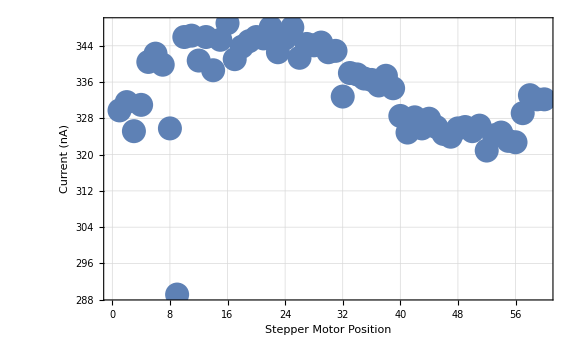

334.621

10.3356

```mathematica
file=ImportFile["POL2018-03-18_042230.dat"];
rev=file[[1]]["REV"];
currentScale=file[[1]]["SCALE"];
currentValues=Normal[file[[2]][All,"CURRENT",Abs]]*10^(-currentScale)/nA
ListPlot[currentValues,FrameLabel->{"Stepper Motor Position","Current (nA)"}]
Mean[currentValues]
StandardDeviation[currentValues]
```